## Construct and Parameterize One Enzyme Module

```mathematica
Quit[]
```

## Initializing the Notebook

```mathematica
<<Toolbox`;
<<MASSef`;

SetDirectory[NotebookDirectory[]];

removeInputFiles = True;
removeOutputFiles = True;

rxnName="IGPS";
fitLabel=rxnName;
dataFileName=rxnName;

assumedUncertaintyFraction = 0.05;
(*Q10 Correction Options*)
Q10KcatCorrectionFlag = True; (*True if kcats should be corrected to physiological T*)
TPhysiological = 37; (*C*)


(* user will need to change this path *)
pathMASSef = "/Users/guest/Desktop/internship stuff/MASSef/";
kineticDataFileName =  "kinetic_data_trp3.csv";

mainFolder = "fit_IGPS_TEST_typeII";
{pathData, inputPath, outputPath}=initializeNotebook[pathMASSef, mainFolder, removeInputFiles, removeOutputFiles];
```

Molecule::shdw: Symbol Molecule appears in multiple contexts {AutomaticUnits`,System`}; definitions in context AutomaticUnits` may shadow or be shadowed by other definitions.

Working dir:/Users/guest/Desktop/internship stuff/MASSef/examples/

## Import Data

```mathematica
{rxn, mechanism, structure, nActiveSites, nAllostericSites, KeqList0,kmList0, s05List0, kcatList0, inhibitionList0, activationList0, otherParmsList0, bufferInfo, ionCharge}= importAllData [rxnName, pathData, kineticDataFileName,  assumedUncertaintyFraction, Q10KcatCorrectionFlag, TPhysiological];
```

{2cpr5p,Null,Keq substrate}

{2.6×10^14,Keq value}

{2cpr5p,Km or S05 substrate}

{1.6×10^-6,Km or S05 value}

{2cpr5p,Km or S05 substrate}

{0.00009,Km or S05 value}

{2cpr5p,Km or S05 substrate}

{3.4×10^-7,Km or S05 value}

{2cpr5p,Km or S05 substrate}

{4.2×10^-7,Km or S05 value}

{2cpr5p,Km or S05 substrate}

{1.2×10^-6,Km or S05 value}

{2cpr5p,Km or S05 substrate}

{5.×10^-6,Km or S05 value}

{2cpr5p,Km or S05 substrate}

{5.8×10^-6,Km or S05 value}

{{{2cpr5p,Null}},kcat substrates}

{1.2,kcat value}

{{{2cpr5p,Null}},kcat substrates}

{4.1,kcat value}

{{{2cpr5p,Null}},kcat substrates}

{9.3,kcat value}

{{{2cpr5p,Null}},kcat substrates}

{2.2,kcat value}

{{{2cpr5p,Null}},kcat substrates}

{3.6,kcat value}

{{{2cpr5p,Null}},kcat substrates}

{7.2,kcat value}

{2cpr5p,Other parameter susbtrate}

{13300,Other parameter value}

{2cpr5p,Other parameter susbtrate}

{570000,Other parameter value}

{2cpr5p,Inhibition or activation constant substrate}

{5.4×10^-7,Inhibition or activation constant value}

((2cpr5p)^c⇌(3ig3p)^c+co2^c)^IGPS

ordered uni-bi; 2cpr5p,c02,3ig3p

Structure: 1

Active sites: 1

Keq Values:

Priority | Substrate | Keq_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | 2cpr5p,Null | 2.6×10^14 | 2.47×10^14
2.73×10^14 | Null | Null | 7.5 | Null | Null | Null

Km Values:

Priority | Substrate | Km_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | 2cpr5p | 1.6×10^-6 | 1.3×10^-6
1.9×10^-6 |  | M | 7.5 | 37 | hepps | 0.05
edta | 0.004 | 
1 | 2cpr5p | 0.00009 | 0.0000855
0.0000945 |  | M | 7.5 | 25 | hepps | 0.05 | 
1 | 2cpr5p | 3.4×10^-7 | 3.23×10^-7
3.57×10^-7 |  | M | 7.5 | 25 | trishcl | 0.05
edta | 0.004 | k | 0.008
mg2 | 0.004
1 | 2cpr5p | 4.2×10^-7 | 3.99×10^-7
4.41×10^-7 |  | M | 7.5 | 25 | trishcl | 0.05
edta | 0.004 | k | 0.008
mg2 | 0.004
1 | 2cpr5p | 1.2×10^-6 | 1.14×10^-6
1.26×10^-6 |  | M | 7.6 | 25 | trishcl | 0.05
edta | 0.005 | 
1 | 2cpr5p | 5.×10^-6 | 4.75×10^-6
5.25×10^-6 |  | M | 7.8 | 37 | trishcl | 0.1 | 
1 | 2cpr5p | 5.8×10^-6 | 5.51×10^-6
6.09×10^-6 |  | M | 7.5 | 37 | trishcl | 0.05 |

S0.5 Values:

Priority | Substrate | S0.5_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

kcat Values:

Priority | Metabolite(s) | Value | Uncertainty | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | 2cpr5p | Null | 3.60337 | 3.4232
3.78354 | 1/s | 7.5 | 37 | hepps | 0.05 | 
1 | 2cpr5p | Null | 12.3115 | 11.6959
12.9271 | 1/s | 7.5 | 37 | hepps | 0.05
edta | 0.004 | 
1 | 2cpr5p | Null | 9.3 | 8.835
9.765 | 1/s | 7.5 | 37 | hepps | 0.05
edta | 0.004 | 
1 | 2cpr5p | Null | 6.60618 | 6.27588
6.93649 | 1/s | 7.5 | 37 | trishcl | 0.05
edta | 0.004 | k | 0.008
mg2 | 0.004
1 | 2cpr5p | Null | 10.8101 | 10.2696
11.3506 | 1/s | 7.5 | 37 | trishcl | 0.05
edta | 0.004 | k | 0.008
mg2 | 0.004
1 | 2cpr5p | Null | 21.6202 | 20.5392
22.7013 | 1/s | 7.6 | 37 | trishcl | 0.05
edta | 0.005 |

Inhibition Values:

Priority | Parameter_Type | Inhibitor | Value | Uncertainty | Cosubstrates | Inhibition Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | Kic | 2cpr5p | 5.4×10^-7 | 5.13×10^-7
5.67×10^-7 |  | Competitive | pran | 4.9×10^-6 | M | 7.5 | 25 | trishcl | 0.05
edta | 0.004 |

Activation Values:

Priority | Parameter_Type | Activator | Value | Uncertainty | Cosubstrates | Activation Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Other Parameters:

Priority | Parameter_Type | Metabolite | Value | Uncertainty | Cosubstrates | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | kcat/Km | 2cpr5p | 13300 | 12635.
13965. |  | 1/(M*s) | 7.5 | 25 | hepps | 0.05 | 
1 | kcat/Km | 2cpr5p | 570000 | 541500.
598500. |  | 1/(M*s) | 7.5 | 37 | hepps | 0.05
edta | 0.004 |

### Define data points priority

```mathematica
(* data point priorities should be between 0 and 1 
  if a given data point has priority 0, it will be discarded
  by default all data points priority is set to 1 *)

KeqPriorities = {1};
kmPriorities = {1,1,1,1,1,1,1};
s05Priorities = Null;
kcatPriorities = {1,1,1,1,1,1};
inhibitionPriorities={0};
activationPriorities = Null;
otherParamsPriorities = {0,0};

{KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList}= updateDataPriorities[KeqPriorities, kmPriorities, s05Priorities, kcatPriorities, inhibitionPriorities, activationPriorities, otherParamsPriorities,
					 KeqList0,kmList0, s05List0, kcatList0, inhibitionList0, activationList0, otherParmsList0];

printEnzymeData[rxn, mechanism, structure, nActiveSites,  KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList];
```

((2cpr5p)^c⇌(3ig3p)^c+co2^c)^IGPS

ordered uni-bi; 2cpr5p,c02,3ig3p

Structure: 1

Active sites: 1

Keq Values:

Priority | Substrate | Keq_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | 2cpr5p,Null | 2.6×10^14 | 2.47×10^14
2.73×10^14 | Null | Null | 7.5 | Null | Null | Null

Km Values:

Priority | Substrate | Km_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | 2cpr5p | 1.6×10^-6 | 1.3×10^-6
1.9×10^-6 |  | M | 7.5 | 37 | hepps | 0.05
edta | 0.004 | 
1 | 2cpr5p | 0.00009 | 0.0000855
0.0000945 |  | M | 7.5 | 25 | hepps | 0.05 | 
1 | 2cpr5p | 3.4×10^-7 | 3.23×10^-7
3.57×10^-7 |  | M | 7.5 | 25 | trishcl | 0.05
edta | 0.004 | k | 0.008
mg2 | 0.004
1 | 2cpr5p | 4.2×10^-7 | 3.99×10^-7
4.41×10^-7 |  | M | 7.5 | 25 | trishcl | 0.05
edta | 0.004 | k | 0.008
mg2 | 0.004
1 | 2cpr5p | 1.2×10^-6 | 1.14×10^-6
1.26×10^-6 |  | M | 7.6 | 25 | trishcl | 0.05
edta | 0.005 | 
1 | 2cpr5p | 5.×10^-6 | 4.75×10^-6
5.25×10^-6 |  | M | 7.8 | 37 | trishcl | 0.1 | 
1 | 2cpr5p | 5.8×10^-6 | 5.51×10^-6
6.09×10^-6 |  | M | 7.5 | 37 | trishcl | 0.05 |

S0.5 Values:

Priority | Substrate | S0.5_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

kcat Values:

Priority | Metabolite(s) | Value | Uncertainty | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | 2cpr5p | Null | 3.60337 | 3.4232
3.78354 | 1/s | 7.5 | 37 | hepps | 0.05 | 
1 | 2cpr5p | Null | 12.3115 | 11.6959
12.9271 | 1/s | 7.5 | 37 | hepps | 0.05
edta | 0.004 | 
1 | 2cpr5p | Null | 9.3 | 8.835
9.765 | 1/s | 7.5 | 37 | hepps | 0.05
edta | 0.004 | 
1 | 2cpr5p | Null | 6.60618 | 6.27588
6.93649 | 1/s | 7.5 | 37 | trishcl | 0.05
edta | 0.004 | k | 0.008
mg2 | 0.004
1 | 2cpr5p | Null | 10.8101 | 10.2696
11.3506 | 1/s | 7.5 | 37 | trishcl | 0.05
edta | 0.004 | k | 0.008
mg2 | 0.004
1 | 2cpr5p | Null | 21.6202 | 20.5392
22.7013 | 1/s | 7.6 | 37 | trishcl | 0.05
edta | 0.005 |

Inhibition Values:

Priority | Parameter_Type | Inhibitor | Value | Uncertainty | Cosubstrates | Inhibition Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Activation Values:

Priority | Parameter_Type | Activator | Value | Uncertainty | Cosubstrates | Activation Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Other Parameters:

Priority | Parameter_Type | Metabolite | Value | Uncertainty | Cosubstrates | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

## Define enzyme mechanism and catalytic tracks

### Define enzyme mechanism

```mathematica
catalyticBranch={"E_IGPS[c] + 2cpr5p[c] <=> E_IGPS[c]&2cpr5p",
				"E_IGPS[c]&2cpr5p <=> E_IGPS[c]&3ig3p&co2",
				"E_IGPS[c]&3ig3p&co2 <=> E_IGPS[c]&3ig3p + co2[c]",
                                            "E_IGPS[c]&3ig3p <=> E_IGPS[c] + 3ig3p[c]"};


enzymeModel=constructEnzymeModule[Mechanism->catalyticBranch,Activators->{},ActivationSites->0,Inhibitors->{},InhibitionSites->0];
enzymeModel["Reactions"]
```

{((IGPS^c)_^+(2cpr5p)^c⇌(IGPS^c&(2cpr5p)^c)_^)^IGPS1,((IGPS^c&(3ig3p)^c)_^⇌(IGPS^c)_^+(3ig3p)^c)^IGPS2,((IGPS^c&(2cpr5p)^c)_^⇌(IGPS^c&(3ig3p)^c&co2^c)_^)^IGPS3,((IGPS^c&(3ig3p)^c&co2^c)_^⇌(IGPS^c&(3ig3p)^c)_^+co2^c)^IGPS4}

### Define all catalytic tracks

```mathematica
catalyticReactionsSet1={((IGPS^c)_^+(2cpr5p)^c⇌(IGPS^c&(2cpr5p)^c)_^)^IGPS1,Overscript[(IGPS^c&(3ig3p)^c)_^⇌(IGPS^c)_^+(3ig3p)^c, IGPS2],((IGPS^c&(2cpr5p)^c)_^⇌(IGPS^c&(3ig3p)^c&co2^c)_^)^IGPS3,Overscript[(IGPS^c&(3ig3p)^c&co2^c)_^⇌(IGPS^c&(3ig3p)^c)_^+co2^c, IGPS4]};
catalyticReactionsSetsList = {catalyticReactionsSet1};
```

## Set up rate equations

```mathematica
MWCFlag=False;
nActiveSites=1;
simplifyFlag=True;
simplifyMaxTime=300;
otherMetsReverseZeroSub={};
 otherMetsForwardZeroSub ={};

{enzymeModel, haldaneRatiosList,  metSatForSub, metSatRevSub,  finalRateConsts, metsFull, metsSub, rateConstsSub, 
			fileList, fileListSub, eqnNameList,eqnValList, eqnValListPy, 
			allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList, 
			absoluteFlux, absoluteRateForward, absoluteRateReverse, relativeRateForward, relativeRateReverse, 
			otherAbsoluteRatesForward, otherAbsoluteRatesReverse}=

	setUpRateEquations[enzymeModel, rxn, rxnName, inputPath, inhibitionList,inhibitionList, catalyticReactionsSetsList, otherMetsReverseZeroSub,  
						 otherMetsForwardZeroSub,  MWCFlag, simplifyFlag, simplifyMaxTime, nActiveSites];
```

{(2cpr5p)^c→0}

{(3ig3p)^c→0,co2^c→0}

{(2cpr5p)^c→∞}

{(3ig3p)^c→∞,co2^c→∞}

Added inhibition reactions:

{}

Generating flux equation...

{((IGPS^c&(2cpr5p)^c)_^-((IGPS^c&(3ig3p)^c&co2^c)_^)/K_IGPS3) Volume_c k_IGPS3^⟶}

Volume_c (-(IGPS^c&(3ig3p)^c&co2^c)_^ k_IGPS3^⟵+(IGPS^c&(2cpr5p)^c)_^ k_IGPS3^⟶)

1

2

3

0.10901

4

0.000454

5

0.00013

Simplifying...

6

0.078055

Generating absolute rate forward equation...

Simplifying...

Generating absolute rate reverse equation...

Simplifying...

Generating relative rate forward equation...

Simplifying...

Generating relative rate reverse equation...

Simplifying...

Generating relative rate reverse equation...

Simplifying...

Generating Haldane Relations...

Defining rate constant and metabolite substitutions for export...

Exporting equations...

## Simulate Data

```mathematica
(* format: {priority, ratio or other custom equation, value, value range (uncertainty) *)
customRatiosDataList={(*{1, (Subscript[k, GAPD1]^⟶Subscript[k, GAPD2]^⟶Subscript[k, GAPD3]^⟶Subscript[k, GAPD4]^⟶Subscript[k, GAPD5]^⟶)/(Subscript[k, GAPD1]^⟵Subscript[k, GAPD2]^⟵Subscript[k, GAPD3]^⟵Subscript[k, GAPD4]^⟵Subscript[k, GAPD5]^⟵), 4.25*10^2,{0.9*4.25*10^2,1.1*4.25*10^2}}*)};
```

### Simulate data without uncertainty

```mathematica
{allFittingData, dataPathList, fileList, fileListSub}= simulateData[enzymeModel,dataFileName, haldaneRatiosList, KeqList, kmList, s05List, kcatList
, inhibitionList, activationList, otherParmsList, rxn, metsFull,  
			metSatForSub, metSatRevSub,  bufferInfo, ionCharge, inputPath,  fileList, fileListSub, 
			eqnNameList,eqnValList, eqnValListPy, eqnNameList, rateConstsSub, 
			metsSub, allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList, customRatiosDataList];
```

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

```mathematica
Print[relativeRateForward]
```

{((2cpr5p)^c k_IGPS1^⟶ (k_IGPS3^⟶ k_IGPS4^⟶+k_IGPS2^⟶ (k_IGPS3^⟵+k_IGPS3^⟶+k_IGPS4^⟶)))/(k_IGPS2^⟶ k_IGPS3^⟶ k_IGPS4^⟶+k_IGPS1^⟵ k_IGPS2^⟶ (k_IGPS3^⟵+k_IGPS4^⟶)+(2cpr5p)^c k_IGPS1^⟶ (k_IGPS3^⟶ k_IGPS4^⟶+k_IGPS2^⟶ (k_IGPS3^⟵+k_IGPS3^⟶+k_IGPS4^⟶)))}

```mathematica
FilePrint@dataPathList
```

Priority	2cpr5p[c]	3ig3p[c]	co2[c]	param_IGPS_total	param_pH	param_Temp	FileFlag	Target_Data
1	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_IGPS_TEST_typeII/input/haldaneRatio_1.txt"	2.6e14
1	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_IGPS_TEST_typeII/input/haldaneRatio_1.txt"	2.6e14
1	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_IGPS_TEST_typeII/input/haldaneRatio_1.txt"	2.6e14
1	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_IGPS_TEST_typeII/input/haldaneRatio_1.txt"	2.6e14
1	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_IGPS_TEST_typeII/input/haldaneRatio_1.txt"	2.6e14
1	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_IGPS_TEST_typeII/input/haldaneRatio_1.txt"	2.6e14
1	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_IGPS_TEST_typeII/input/haldaneRatio_1.txt"	2.6e14
1	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_IGPS_TEST_typeII/input/haldaneRatio_1.txt"	2.6e14
1	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_IGPS_TEST_typeII/input/haldaneRatio_1.txt"	2.6e14
1	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_IGPS_TEST_typeII/input/haldaneRatio_1.txt"	2.6e14
1	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_IGPS_TEST_typeII/input/haldaneRatio_1.txt"	2.6e14
1	1.6000000000000008e-7	0	0	1	7.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_IGPS_TEST_typeII/input/relRateFor_2cpr5p.txt"	0.09090909090909094
1	2.535829107937784e-7	0	0	1	7.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_IGPS_TEST_typeII/input/relRateFor_2cpr5p.txt"	0.1368068886032101
1	4.0190182904153334e-7	0	0	1	7.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_IGPS_TEST_typeII/input/relRateFor_2cpr5p.txt"	0.20076000891310194
1	6.369714728855955e-7	0	0	1	7.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_IGPS_TEST_typeII/input/relRateFor_2cpr5p.txt"	0.28474724895080133
1	1.0095317511683094e-6	0	0	1	7.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_IGPS_TEST_typeII/input/relRateFor_2cpr5p.txt"	0.386863179846857
1	1.6000000000000008e-6	0	0	1	7.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_IGPS_TEST_typeII/input/relRateFor_2cpr5p.txt"	0.5000000000000001
1	2.535829107937784e-6	0	0	1	7.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_IGPS_TEST_typeII/input/relRateFor_2cpr5p.txt"	0.6131368201531432
1	4.019018290415333e-6	0	0	1	7.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_IGPS_TEST_typeII/input/relRateFor_2cpr5p.txt"	0.7152527510491988
1	6.369714728855954e-6	0	0	1	7.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_IGPS_TEST_typeII/input/relRateFor_2cpr5p.txt"	0.7992399910868981
1	0.000010095317511683093	0	0	1	7.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_IGPS_TEST_typeII/input/relRateFor_2cpr5p.txt"	0.86319311139679
1	0.00001600000000000001	0	0	1	7.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_IGPS_TEST_typeII/input/relRateFor_2cpr5p.txt"	0.9090909090909093
1	9.000000000000007e-6	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_IGPS_TEST_typeII/input/relRateFor_2cpr5p.txt"	0.09090909090909098
1	0.000014264038732150038	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_IGPS_TEST_typeII/input/relRateFor_2cpr5p.txt"	0.13680688860321014
1	0.000022606977883586257	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_IGPS_TEST_typeII/input/relRateFor_2cpr5p.txt"	0.20076000891310197
1	0.00003582964534981475	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_IGPS_TEST_typeII/input/relRateFor_2cpr5p.txt"	0.2847472489508014
1	0.00005678616100321741	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_IGPS_TEST_typeII/input/relRateFor_2cpr5p.txt"	0.38686317984685703
1	0.00009000000000000007	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_IGPS_TEST_typeII/input/relRateFor_2cpr5p.txt"	0.5000000000000002
1	0.00014264038732150037	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_IGPS_TEST_typeII/input/relRateFor_2cpr5p.txt"	0.6131368201531432
1	0.00022606977883586258	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_IGPS_TEST_typeII/input/relRateFor_2cpr5p.txt"	0.7152527510491988
1	0.00035829645349814786	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_IGPS_TEST_typeII/input/relRateFor_2cpr5p.txt"	0.7992399910868985
1	0.0005678616100321741	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_IGPS_TEST_typeII/input/relRateFor_2cpr5p.txt"	0.86319311139679
1	0.0009000000000000007	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_IGPS_TEST_typeII/input/relRateFor_2cpr5p.txt"	0.9090909090909093
1	3.400000000000002e-8	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_IGPS_TEST_typeII/input/relRateFor_2cpr5p.txt"	0.09090909090909097
1	5.388636854367791e-8	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_IGPS_TEST_typeII/input/relRateFor_2cpr5p.txt"	0.13680688860321014
1	8.540413867132583e-8	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_IGPS_TEST_typeII/input/relRateFor_2cpr5p.txt"	0.20076000891310197
1	1.3535643798818904e-7	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_IGPS_TEST_typeII/input/relRateFor_2cpr5p.txt"	0.2847472489508014
1	2.1452549712326574e-7	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_IGPS_TEST_typeII/input/relRateFor_2cpr5p.txt"	0.386863179846857
1	3.400000000000002e-7	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_IGPS_TEST_typeII/input/relRateFor_2cpr5p.txt"	0.5000000000000002
1	5.388636854367791e-7	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_IGPS_TEST_typeII/input/relRateFor_2cpr5p.txt"	0.6131368201531433
1	8.540413867132584e-7	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_IGPS_TEST_typeII/input/relRateFor_2cpr5p.txt"	0.7152527510491988
1	1.3535643798818904e-6	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_IGPS_TEST_typeII/input/relRateFor_2cpr5p.txt"	0.7992399910868982
1	2.1452549712326573e-6	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_IGPS_TEST_typeII/input/relRateFor_2cpr5p.txt"	0.8631931113967899
1	3.4000000000000018e-6	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_IGPS_TEST_typeII/input/relRateFor_2cpr5p.txt"	0.909090909090909
1	4.200000000000003e-8	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_IGPS_TEST_typeII/input/relRateFor_2cpr5p.txt"	0.09090909090909097
1	6.656551408336685e-8	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_IGPS_TEST_typeII/input/relRateFor_2cpr5p.txt"	0.13680688860321014
1	1.0549923012340253e-7	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_IGPS_TEST_typeII/input/relRateFor_2cpr5p.txt"	0.20076000891310197
1	1.6720501163246884e-7	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_IGPS_TEST_typeII/input/relRateFor_2cpr5p.txt"	0.2847472489508014
1	2.6500208468168126e-7	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_IGPS_TEST_typeII/input/relRateFor_2cpr5p.txt"	0.38686317984685703
1	4.200000000000003e-7	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_IGPS_TEST_typeII/input/relRateFor_2cpr5p.txt"	0.5000000000000002
1	6.656551408336684e-7	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_IGPS_TEST_typeII/input/relRateFor_2cpr5p.txt"	0.6131368201531433
1	1.0549923012340252e-6	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_IGPS_TEST_typeII/input/relRateFor_2cpr5p.txt"	0.7152527510491988
1	1.6720501163246882e-6	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_IGPS_TEST_typeII/input/relRateFor_2cpr5p.txt"	0.7992399910868982
1	2.6500208468168126e-6	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_IGPS_TEST_typeII/input/relRateFor_2cpr5p.txt"	0.8631931113967901
1	4.200000000000003e-6	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_IGPS_TEST_typeII/input/relRateFor_2cpr5p.txt"	0.9090909090909092
1	1.2000000000000007e-7	0	0	1	7.6	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_IGPS_TEST_typeII/input/relRateFor_2cpr5p.txt"	0.09090909090909097
1	1.901871830953338e-7	0	0	1	7.6	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_IGPS_TEST_typeII/input/relRateFor_2cpr5p.txt"	0.1368068886032101
1	3.014263717811501e-7	0	0	1	7.6	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_IGPS_TEST_typeII/input/relRateFor_2cpr5p.txt"	0.20076000891310197
1	4.777286046641966e-7	0	0	1	7.6	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_IGPS_TEST_typeII/input/relRateFor_2cpr5p.txt"	0.2847472489508014
1	7.571488133762321e-7	0	0	1	7.6	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_IGPS_TEST_typeII/input/relRateFor_2cpr5p.txt"	0.38686317984685703
1	1.2000000000000008e-6	0	0	1	7.6	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_IGPS_TEST_typeII/input/relRateFor_2cpr5p.txt"	0.5000000000000001
1	1.9018718309533382e-6	0	0	1	7.6	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_IGPS_TEST_typeII/input/relRateFor_2cpr5p.txt"	0.6131368201531433
1	3.0142637178115004e-6	0	0	1	7.6	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_IGPS_TEST_typeII/input/relRateFor_2cpr5p.txt"	0.7152527510491989
1	4.777286046641966e-6	0	0	1	7.6	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_IGPS_TEST_typeII/input/relRateFor_2cpr5p.txt"	0.7992399910868984
1	7.571488133762321e-6	0	0	1	7.6	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_IGPS_TEST_typeII/input/relRateFor_2cpr5p.txt"	0.86319311139679
1	0.000012000000000000007	0	0	1	7.6	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_IGPS_TEST_typeII/input/relRateFor_2cpr5p.txt"	0.9090909090909092
1	5.e-7	0	0	1	7.8	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_IGPS_TEST_typeII/input/relRateFor_2cpr5p.txt"	0.0909090909090909
1	7.924465962305569e-7	0	0	1	7.8	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_IGPS_TEST_typeII/input/relRateFor_2cpr5p.txt"	0.13680688860321003
1	1.255943215754791e-6	0	0	1	7.8	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_IGPS_TEST_typeII/input/relRateFor_2cpr5p.txt"	0.20076000891310183
1	1.9905358527674846e-6	0	0	1	7.8	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_IGPS_TEST_typeII/input/relRateFor_2cpr5p.txt"	0.2847472489508012
1	3.1547867224009644e-6	0	0	1	7.8	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_IGPS_TEST_typeII/input/relRateFor_2cpr5p.txt"	0.3868631798468568
1	4.9999999999999996e-6	0	0	1	7.8	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_IGPS_TEST_typeII/input/relRateFor_2cpr5p.txt"	0.5
1	7.924465962305569e-6	0	0	1	7.8	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_IGPS_TEST_typeII/input/relRateFor_2cpr5p.txt"	0.6131368201531431
1	0.00001255943215754791	0	0	1	7.8	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_IGPS_TEST_typeII/input/relRateFor_2cpr5p.txt"	0.7152527510491988
1	0.000019905358527674844	0	0	1	7.8	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_IGPS_TEST_typeII/input/relRateFor_2cpr5p.txt"	0.799239991086898
1	0.000031547867224009646	0	0	1	7.8	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_IGPS_TEST_typeII/input/relRateFor_2cpr5p.txt"	0.8631931113967899
1	0.000049999999999999996	0	0	1	7.8	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_IGPS_TEST_typeII/input/relRateFor_2cpr5p.txt"	0.9090909090909091
1	5.799999999999995e-7	0	0	1	7.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_IGPS_TEST_typeII/input/relRateFor_2cpr5p.txt"	0.09090909090909083
1	9.192380516274454e-7	0	0	1	7.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_IGPS_TEST_typeII/input/relRateFor_2cpr5p.txt"	0.13680688860320994
1	1.4568941302755564e-6	0	0	1	7.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_IGPS_TEST_typeII/input/relRateFor_2cpr5p.txt"	0.20076000891310175
1	2.3090215892102803e-6	0	0	1	7.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_IGPS_TEST_typeII/input/relRateFor_2cpr5p.txt"	0.28474724895080106
1	3.6595525979851162e-6	0	0	1	7.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_IGPS_TEST_typeII/input/relRateFor_2cpr5p.txt"	0.38686317984685664
1	5.7999999999999944e-6	0	0	1	7.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_IGPS_TEST_typeII/input/relRateFor_2cpr5p.txt"	0.49999999999999983
1	9.192380516274454e-6	0	0	1	7.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_IGPS_TEST_typeII/input/relRateFor_2cpr5p.txt"	0.6131368201531429
1	0.000014568941302755563	0	0	1	7.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_IGPS_TEST_typeII/input/relRateFor_2cpr5p.txt"	0.7152527510491986
1	0.0000230902158921028	0	0	1	7.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_IGPS_TEST_typeII/input/relRateFor_2cpr5p.txt"	0.7992399910868979
1	0.00003659552597985116	0	0	1	7.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_IGPS_TEST_typeII/input/relRateFor_2cpr5p.txt"	0.8631931113967899
1	0.000057999999999999946	0	0	1	7.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_IGPS_TEST_typeII/input/relRateFor_2cpr5p.txt"	0.909090909090909
1	0.01	0	0	1	7.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_IGPS_TEST_typeII/input/absRateFor.txt"	3.6033733019442944
1	0.01	0	0	1	7.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_IGPS_TEST_typeII/input/absRateFor.txt"	3.6033733019442944
1	0.01	0	0	1	7.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_IGPS_TEST_typeII/input/absRateFor.txt"	3.6033733019442944
1	0.01	0	0	1	7.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_IGPS_TEST_typeII/input/absRateFor.txt"	3.6033733019442944
1	0.01	0	0	1	7.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_IGPS_TEST_typeII/input/absRateFor.txt"	3.6033733019442944
1	0.01	0	0	1	7.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_IGPS_TEST_typeII/input/absRateFor.txt"	3.6033733019442944
1	0.01	0	0	1	7.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_IGPS_TEST_typeII/input/absRateFor.txt"	3.6033733019442944
1	0.01	0	0	1	7.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_IGPS_TEST_typeII/input/absRateFor.txt"	3.6033733019442944
1	0.01	0	0	1	7.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_IGPS_TEST_typeII/input/absRateFor.txt"	3.6033733019442944
1	0.01	0	0	1	7.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_IGPS_TEST_typeII/input/absRateFor.txt"	3.6033733019442944
1	0.01	0	0	1	7.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_IGPS_TEST_typeII/input/absRateFor.txt"	3.6033733019442944
1	0.01	0	0	1	7.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_IGPS_TEST_typeII/input/absRateFor.txt"	12.311525448309672
1	0.01	0	0	1	7.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_IGPS_TEST_typeII/input/absRateFor.txt"	12.311525448309672
1	0.01	0	0	1	7.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_IGPS_TEST_typeII/input/absRateFor.txt"	12.311525448309672
1	0.01	0	0	1	7.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_IGPS_TEST_typeII/input/absRateFor.txt"	12.311525448309672
1	0.01	0	0	1	7.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_IGPS_TEST_typeII/input/absRateFor.txt"	12.311525448309672
1	0.01	0	0	1	7.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_IGPS_TEST_typeII/input/absRateFor.txt"	12.311525448309672
1	0.01	0	0	1	7.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_IGPS_TEST_typeII/input/absRateFor.txt"	12.311525448309672
1	0.01	0	0	1	7.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_IGPS_TEST_typeII/input/absRateFor.txt"	12.311525448309672
1	0.01	0	0	1	7.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_IGPS_TEST_typeII/input/absRateFor.txt"	12.311525448309672
1	0.01	0	0	1	7.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_IGPS_TEST_typeII/input/absRateFor.txt"	12.311525448309672
1	0.01	0	0	1	7.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_IGPS_TEST_typeII/input/absRateFor.txt"	12.311525448309672
1	0.01	0	0	1	7.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_IGPS_TEST_typeII/input/absRateFor.txt"	9.3
1	0.01	0	0	1	7.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_IGPS_TEST_typeII/input/absRateFor.txt"	9.3
1	0.01	0	0	1	7.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_IGPS_TEST_typeII/input/absRateFor.txt"	9.3
1	0.01	0	0	1	7.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_IGPS_TEST_typeII/input/absRateFor.txt"	9.3
1	0.01	0	0	1	7.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_IGPS_TEST_typeII/input/absRateFor.txt"	9.3
1	0.01	0	0	1	7.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_IGPS_TEST_typeII/input/absRateFor.txt"	9.3
1	0.01	0	0	1	7.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_IGPS_TEST_typeII/input/absRateFor.txt"	9.3
1	0.01	0	0	1	7.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_IGPS_TEST_typeII/input/absRateFor.txt"	9.3
1	0.01	0	0	1	7.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_IGPS_TEST_typeII/input/absRateFor.txt"	9.3
1	0.01	0	0	1	7.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_IGPS_TEST_typeII/input/absRateFor.txt"	9.3
1	0.01	0	0	1	7.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_IGPS_TEST_typeII/input/absRateFor.txt"	9.3
1	0.01	0	0	1	7.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_IGPS_TEST_typeII/input/absRateFor.txt"	6.606184386897874
1	0.01	0	0	1	7.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_IGPS_TEST_typeII/input/absRateFor.txt"	6.606184386897874
1	0.01	0	0	1	7.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_IGPS_TEST_typeII/input/absRateFor.txt"	6.606184386897874
1	0.01	0	0	1	7.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_IGPS_TEST_typeII/input/absRateFor.txt"	6.606184386897874
1	0.01	0	0	1	7.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_IGPS_TEST_typeII/input/absRateFor.txt"	6.606184386897874
1	0.01	0	0	1	7.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_IGPS_TEST_typeII/input/absRateFor.txt"	6.606184386897874
1	0.01	0	0	1	7.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_IGPS_TEST_typeII/input/absRateFor.txt"	6.606184386897874
1	0.01	0	0	1	7.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_IGPS_TEST_typeII/input/absRateFor.txt"	6.606184386897874
1	0.01	0	0	1	7.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_IGPS_TEST_typeII/input/absRateFor.txt"	6.606184386897874
1	0.01	0	0	1	7.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_IGPS_TEST_typeII/input/absRateFor.txt"	6.606184386897874
1	0.01	0	0	1	7.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_IGPS_TEST_typeII/input/absRateFor.txt"	6.606184386897874
1	0.01	0	0	1	7.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_IGPS_TEST_typeII/input/absRateFor.txt"	10.810119905832885
1	0.01	0	0	1	7.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_IGPS_TEST_typeII/input/absRateFor.txt"	10.810119905832885
1	0.01	0	0	1	7.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_IGPS_TEST_typeII/input/absRateFor.txt"	10.810119905832885
1	0.01	0	0	1	7.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_IGPS_TEST_typeII/input/absRateFor.txt"	10.810119905832885
1	0.01	0	0	1	7.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_IGPS_TEST_typeII/input/absRateFor.txt"	10.810119905832885
1	0.01	0	0	1	7.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_IGPS_TEST_typeII/input/absRateFor.txt"	10.810119905832885
1	0.01	0	0	1	7.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_IGPS_TEST_typeII/input/absRateFor.txt"	10.810119905832885
1	0.01	0	0	1	7.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_IGPS_TEST_typeII/input/absRateFor.txt"	10.810119905832885
1	0.01	0	0	1	7.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_IGPS_TEST_typeII/input/absRateFor.txt"	10.810119905832885
1	0.01	0	0	1	7.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_IGPS_TEST_typeII/input/absRateFor.txt"	10.810119905832885
1	0.01	0	0	1	7.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_IGPS_TEST_typeII/input/absRateFor.txt"	10.810119905832885
1	0.01	0	0	1	7.6	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_IGPS_TEST_typeII/input/absRateFor.txt"	21.62023981166577
1	0.01	0	0	1	7.6	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_IGPS_TEST_typeII/input/absRateFor.txt"	21.62023981166577
1	0.01	0	0	1	7.6	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_IGPS_TEST_typeII/input/absRateFor.txt"	21.62023981166577
1	0.01	0	0	1	7.6	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_IGPS_TEST_typeII/input/absRateFor.txt"	21.62023981166577
1	0.01	0	0	1	7.6	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_IGPS_TEST_typeII/input/absRateFor.txt"	21.62023981166577
1	0.01	0	0	1	7.6	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_IGPS_TEST_typeII/input/absRateFor.txt"	21.62023981166577
1	0.01	0	0	1	7.6	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_IGPS_TEST_typeII/input/absRateFor.txt"	21.62023981166577
1	0.01	0	0	1	7.6	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_IGPS_TEST_typeII/input/absRateFor.txt"	21.62023981166577
1	0.01	0	0	1	7.6	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_IGPS_TEST_typeII/input/absRateFor.txt"	21.62023981166577
1	0.01	0	0	1	7.6	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_IGPS_TEST_typeII/input/absRateFor.txt"	21.62023981166577
1	0.01	0	0	1	7.6	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_IGPS_TEST_typeII/input/absRateFor.txt"	21.62023981166577

### Simulate data with uncertainty

```mathematica
nSamples=10;
SeedRandom[1234];
{allFittingDataList, dataPathList, fileList, fileListSub}=simulateDataWithUncertainty[nSamples,enzymeModel,dataFileName, haldaneRatiosList, KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList, rxn, metsFull,  metSatForSub, metSatRevSub, otherParmsList,  bufferInfo, ionCharge, inputPath,  fileList, 
							fileListSub, eqnNameList,eqnValList, eqnValListPy, eqnNameList, rateConstsSub, 
							metsSub, allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList,  customRatiosDataList];
```

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

```mathematica
FilePrint[dataPathList[[1]]]
```

Priority	13dpg[c]	g3p[c]	nad[c]	nadh[c]	pi[c]	param_GAPD_total	param_pH	param_Temp	FileFlag	Target_Data
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0.089	3.8624414067610525e-6	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.09090909090909095
1	0	0.089	6.1215570918555205e-6	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.1368068886032101
1	0	0.089	9.702014162143871e-6	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.20076000891310197
1	0	0.089	0.00001537665619874311	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.2847472489508014
1	0	0.089	0.000024370357732202946	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.38686317984685703
1	0	0.089	0.00003862441406761052	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.5000000000000001
1	0	0.089	0.0000612155709185552	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.6131368201531432
1	0	0.089	0.0000970201416214387	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.7152527510491988
1	0	0.089	0.00015376656198743123	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.7992399910868984
1	0	0.089	0.00024370357732202944	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.86319311139679
1	0	0.089	0.00038624414067610526	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.9090909090909091
0.7	0	0.0001345263278918314	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.09090909090909088
0.7	0	0.0002132098612825553	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.13680688860321
0.7	0	0.00033791485771230003	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.20076000891310167
0.7	0	0.0005355589576196904	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.2847472489508014
0.7	0	0.0008488037460930167	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.3868631798468568
0.7	0	0.0013452632789183142	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.49999999999999994
0.7	0	0.002132098612825553	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.613136820153143
0.7	0	0.0033791485771230037	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.7152527510491987
0.7	0	0.005355589576196904	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.7992399910868981
0.7	0	0.008488037460930166	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.8631931113967899
0.7	0	0.013452632789183142	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.909090909090909
1	0	0.089	0.0045	0	0.00004095978570257995	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.0909090909090909
1	0	0.089	0.0045	0	0.00006491688552468503	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.13680688860321005
1	0	0.089	0.0045	0	0.00010288632994385063	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.20076000891310167
1	0	0.089	0.0045	0	0.00016306384392531697	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.2847472489508014
1	0	0.089	0.0045	0	0.0002584387761737762	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.3868631798468568
1	0	0.089	0.0045	0	0.00040959785702579944	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.5
1	0	0.089	0.0045	0	0.0006491688552468503	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.6131368201531432
1	0	0.089	0.0045	0	0.0010288632994385075	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.7152527510491987
1	0	0.089	0.0045	0	0.0016306384392531697	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.7992399910868982
1	0	0.089	0.0045	0	0.002584387761737762	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.86319311139679
1	0	0.089	0.0045	0	0.004095978570257995	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.9090909090909091
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268.6249933354222
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268.6249933354222
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268.6249933354222
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268.6249933354222
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268.6249933354222
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268.6249933354222
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268.6249933354222
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268.6249933354222
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268.6249933354222
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268.6249933354222
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268.6249933354222
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.

### Parameter scan

```mathematica
paramScanList={{"Km",1,{0.1,1,100}},
				{"Km",2,{0.01,1,100}},
				{"Km",3,{0.01,10,100}},
				{"kcat",1,{0.01,1,100}},
				{"customRatio",1,{0.01,1,100}},
				{"Keq",1,{0.01,0.1,100}},
				{"other",1,{10^-8,10.^-6,10^-4}}};

{allFittingDataList, dataPathList, fileList, fileListSub}=simulateParameterScanData[paramScanList, enzymeModel, dataFileName, 
						  haldaneRatiosList, KeqList, kmList, s05List, kcatList, inhibitionList, activationList, 
						  otherParmsList, rxn, metsFull, metSatForSub, metSatRevSub,  bufferInfo, 
						  ionCharge, inputPath, fileList, fileListSub, eqnNameList, 
						  eqnValList, eqnValListPy, eqnNameList, rateConstsSub, metsSub, allCatalyticReactions,
						  nonCatalyticReactions, unifiedRateConstList, customRatiosDataList];
```

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

```mathematica
FilePrint[dataPathList[[18]]]
```

Priority	13dpg[c]	g3p[c]	nad[c]	nadh[c]	pi[c]	param_GAPD_total	param_pH	param_Temp	FileFlag	Target_Data
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0.089	4.500000000000003e-6	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.09090909090909095
1	0	0.089	7.132019366075018e-6	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.13680688860321014
1	0	0.089	0.000011303488941793127	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.20076000891310194
1	0	0.089	0.000017914822674907372	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.28474724895080133
1	0	0.089	0.000028393080501608703	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.386863179846857
1	0	0.089	0.00004500000000000003	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.5000000000000002
1	0	0.089	0.00007132019366075018	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.6131368201531432
1	0	0.089	0.00011303488941793127	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.7152527510491989
1	0	0.089	0.0001791482267490739	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.7992399910868984
1	0	0.089	0.00028393080501608705	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.86319311139679
1	0	0.089	0.00045000000000000026	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.9090909090909093
0.7	0	0.00008900000000000009	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.090909090909091
0.7	0	0.00014105549412903932	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.1368068886032102
0.7	0	0.00022355789240435282	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.2007600089131019
0.7	0	0.000354315381792613	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.2847472489508017
0.7	0	0.0005615520365873723	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.3868631798468571
0.7	0	0.0008900000000000009	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.5000000000000003
0.7	0	0.0014105549412903931	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.6131368201531434
0.7	0	0.0022355789240435303	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.7152527510491988
0.7	0	0.00354315381792613	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.7992399910868984
0.7	0	0.005615520365873723	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.86319311139679
0.7	0	0.008900000000000009	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.9090909090909092
1	0	0.089	0.0045	0	0.000053000000000000014	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.09090909090909094
1	0	0.089	0.0045	0	0.00008399933920043907	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.13680688860321008
1	0	0.089	0.0045	0	0.00013312998087000775	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.20076000891310175
1	0	0.089	0.0045	0	0.00021099680039335364	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.2847472489508015
1	0	0.089	0.0045	0	0.00033440739257450236	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.3868631798468569
1	0	0.089	0.0045	0	0.0005300000000000001	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.5
1	0	0.089	0.0045	0	0.0008399933920043907	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.6131368201531432
1	0	0.089	0.0045	0	0.0013312998087000789	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.7152527510491988
1	0	0.089	0.0045	0	0.0021099680039335365	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.7992399910868982
1	0	0.089	0.0045	0	0.0033440739257450235	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.8631931113967899
1	0	0.089	0.0045	0	0.005300000000000002	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.9090909090909092
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.

## Configure the Particle Swarm Optimization and Levenberg-Marquardt Algorithm

```mathematica
numFits=5;
lowerParamBound=-6;
upperParamBound=9;
{psoParameterPath,psoResultsFile, psoTrialSummaryFileName}  = 
definePSOparameters[inputPath, outputPath, finalRateConsts, fileList, numFits,lowerParamBound, upperParamBound, fitLabel];
{lmaParameterPath, lmaResultsFile} = defineLMAparameters[inputPath, outputPath, finalRateConsts, fileList, lowerParamBound, upperParamBound, fitLabel];
```

```mathematica
(*Print the Parameter File (Optional) *)
FilePrint[psoParameterPath]
```

num_Cpus	1
temperature_correction	False
num_trial	5
num_generations	2000
val_pop_size	20
bestFitnessCutoff	1.1
val_neigh_size	3
val_inertia	1
val_cogn_rate	2.1
val_soc_rate	2.1
use_Keep_Best	True
use_Random_Replace	True
percent_Rand	0.05
lower_bound	-6
upper_bound	9
num_func_var	8
filesWithFunctions	[/Users/guest/Desktop/internship stuff/MASSef/examples/fit_IGPS_TEST_typeII/input/absRateFor.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_IGPS_TEST_typeII/input/absRateRev.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_IGPS_TEST_typeII/input/relRateFor_2cpr5p.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_IGPS_TEST_typeII/input/relRateRev_3ig3p.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_IGPS_TEST_typeII/input/relRateRev_co2.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_IGPS_TEST_typeII/input/haldaneRatio_1.txt]
value_row	-1
function_row	-2
data_row_high	-2

```mathematica
(*Optional*)
FilePrint[lmaParameterPath]
```

num_Cpus	1
temperature_correction	False
xtol_value	1.e-15
ftol_value	1.e-7
gtol_value	1.e-7
epsfcn_min_value	7
maxfev_value	1000
lower_bound	-6
upper_bound	9
num_func_var	8
filesWithFunctions	[/Users/guest/Desktop/internship stuff/MASSef/examples/fit_IGPS_TEST_typeII/input/absRateFor.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_IGPS_TEST_typeII/input/absRateRev.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_IGPS_TEST_typeII/input/relRateFor_2cpr5p.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_IGPS_TEST_typeII/input/relRateRev_3ig3p.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_IGPS_TEST_typeII/input/relRateRev_co2.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_IGPS_TEST_typeII/input/haldaneRatio_1.txt]
value_row	-1
function_row	-2
data_row_high	-2

## Fit the model

```mathematica
runFit[inputPath, pathMASSef, psoParameterPath ,lmaParameterPath,psoTrialSummaryFileName, 
		psoResultsFile, lmaResultsFile, numFits, dataPathList]
```

best_fit: 10.6451762788
best_fit: 10.6451762851
best_fit: 10.6451764156
best_fit: 10.6451763974
best_fit: 10.6451762791

## Evaluate fit results

```mathematica
(* run for simple simulated data, no uncertainty or parameter scan*)
lmaResultsFileNew=lmaResultsFile;
dataFilePath = dataPathList;
```

```mathematica
(* run only for data simulated with uncertainty or parameter scan *)
datasetI=2;
lmaResultsFileNew=StringTake[lmaResultsFile,;;-5]<>"_"<>ToString[datasetI] <>".txt";
dataFilePath = dataPathList[[datasetI]];
```

Part::partd: Part specification /Users/guest/Desktop/internship stuff/MASSef/examples/fit_SHK3Dr_TEST_typeII/input/SHK3Dr.dat⟦2⟧ is longer than depth of object.

```mathematica
flagFitType = "abs_ssd";
{flagFitLocal, msgLocal, fittingData, filteredDataList, bestFitDetails}=getRatesWithSSD[rxnName, lmaResultsFileNew, dataFilePath, inputPath, outputPath,  fileListSub, rateConstsSub, metsSub, flagFitType, Null, True, ""];
```

```mathematica
bestFitDetails//TableForm
```

Priority | Fitting Equation | Log10 residual | Log10 residual^2 | Euclidean residual | Relative error | True value | Predicted Value
 |  |  |  |  |  |  | 
1 | haldaneRatio_1 | 4.63338×10^-6 | 2.14682×10^-11 | 2.77386×10^9 | 0.00106687 | 2.6×10^14 | 2.59997×10^14
1 | haldaneRatio_1 | 4.63338×10^-6 | 2.14682×10^-11 | 2.77386×10^9 | 0.00106687 | 2.6×10^14 | 2.59997×10^14
1 | haldaneRatio_1 | 4.63338×10^-6 | 2.14682×10^-11 | 2.77386×10^9 | 0.00106687 | 2.6×10^14 | 2.59997×10^14
1 | haldaneRatio_1 | 4.63338×10^-6 | 2.14682×10^-11 | 2.77386×10^9 | 0.00106687 | 2.6×10^14 | 2.59997×10^14
1 | haldaneRatio_1 | 4.63338×10^-6 | 2.14682×10^-11 | 2.77386×10^9 | 0.00106687 | 2.6×10^14 | 2.59997×10^14
1 | haldaneRatio_1 | 4.63338×10^-6 | 2.14682×10^-11 | 2.77386×10^9 | 0.00106687 | 2.6×10^14 | 2.59997×10^14
1 | haldaneRatio_1 | 4.63338×10^-6 | 2.14682×10^-11 | 2.77386×10^9 | 0.00106687 | 2.6×10^14 | 2.59997×10^14
1 | haldaneRatio_1 | 4.63338×10^-6 | 2.14682×10^-11 | 2.77386×10^9 | 0.00106687 | 2.6×10^14 | 2.59997×10^14
1 | haldaneRatio_1 | 4.63338×10^-6 | 2.14682×10^-11 | 2.77386×10^9 | 0.00106687 | 2.6×10^14 | 2.59997×10^14
1 | haldaneRatio_1 | 4.63338×10^-6 | 2.14682×10^-11 | 2.77386×10^9 | 0.00106687 | 2.6×10^14 | 2.59997×10^14
1 | haldaneRatio_1 | 4.63338×10^-6 | 2.14682×10^-11 | 2.77386×10^9 | 0.00106687 | 2.6×10^14 | 2.59997×10^14
1 | relRateFor_2cpr5p | 0.229028 | 0.052454 | 0.0631317 | 69.4448 | 0.0909091 | 0.154041
1 | relRateFor_2cpr5p | 0.214062 | 0.0458227 | 0.087153 | 63.7052 | 0.136807 | 0.22396
1 | relRateFor_2cpr5p | 0.194033 | 0.0376489 | 0.113082 | 56.3268 | 0.20076 | 0.313842
1 | relRateFor_2cpr5p | 0.169059 | 0.0285811 | 0.135514 | 47.5908 | 0.284747 | 0.420261
1 | relRateFor_2cpr5p | 0.14051 | 0.0197432 | 0.147785 | 38.2008 | 0.386863 | 0.534648
1 | relRateFor_2cpr5p | 0.110928 | 0.0123051 | 0.145503 | 29.1007 | 0.5 | 0.645503
1 | relRateFor_2cpr5p | 0.0832335 | 0.00692782 | 0.129525 | 21.1249 | 0.613137 | 0.742662
1 | relRateFor_2cpr5p | 0.0596679 | 0.00356025 | 0.105339 | 14.7276 | 0.715253 | 0.820592
1 | relRateFor_2cpr5p | 0.0412006 | 0.00169749 | 0.0795352 | 9.95135 | 0.79924 | 0.878775
1 | relRateFor_2cpr5p | 0.0276469 | 0.000764352 | 0.0567371 | 6.57293 | 0.863193 | 0.91993
1 | relRateFor_2cpr5p | 0.018174 | 0.000330295 | 0.0388502 | 4.27352 | 0.909091 | 0.947941
1 | relRateFor_2cpr5p | 1.00094 | 1.00187 | 0.820143 | 902.158 | 0.0909091 | 0.911052
1 | relRateFor_2cpr5p | 0.837931 | 0.702128 | 0.805166 | 588.542 | 0.136807 | 0.941973
1 | relRateFor_2cpr5p | 0.680762 | 0.463438 | 0.761826 | 379.471 | 0.20076 | 0.962586
1 | relRateFor_2cpr5p | 0.535018 | 0.286245 | 0.691316 | 242.782 | 0.284747 | 0.976063
1 | relRateFor_2cpr5p | 0.405774 | 0.164653 | 0.597899 | 154.551 | 0.386863 | 0.984762
1 | relRateFor_2cpr5p | 0.29681 | 0.0880965 | 0.490331 | 98.0662 | 0.5 | 0.990331
1 | relRateFor_2cpr5p | 0.209775 | 0.0440058 | 0.380741 | 62.0972 | 0.613137 | 0.993878
1 | relRateFor_2cpr5p | 0.143856 | 0.0206945 | 0.280876 | 39.2694 | 0.715253 | 0.996128
1 | relRateFor_2cpr5p | 0.096259 | 0.0092658 | 0.198314 | 24.8128 | 0.79924 | 0.997554
1 | relRateFor_2cpr5p | 0.0632205 | 0.00399684 | 0.135262 | 15.6699 | 0.863193 | 0.998455
1 | relRateFor_2cpr5p | 0.0409689 | 0.00167845 | 0.0899337 | 9.89271 | 0.909091 | 0.999025
1 | relRateFor_2cpr5p | 0.38745 | 0.150117 | 0.0536564 | 59.0221 | 0.0909091 | 0.0372527
1 | relRateFor_2cpr5p | 0.374312 | 0.140109 | 0.0790244 | 57.7635 | 0.136807 | 0.0577825
1 | relRateFor_2cpr5p | 0.355316 | 0.126249 | 0.112175 | 55.8751 | 0.20076 | 0.0885852
1 | relRateFor_2cpr5p | 0.329037 | 0.108265 | 0.151265 | 53.1226 | 0.284747 | 0.133482
1 | relRateFor_2cpr5p | 0.294783 | 0.0868969 | 0.190629 | 49.2756 | 0.386863 | 0.196234
1 | relRateFor_2cpr5p | 0.253383 | 0.0642029 | 0.221011 | 44.2022 | 0.5 | 0.278989
1 | relRateFor_2cpr5p | 0.207617 | 0.0431047 | 0.232999 | 38.0012 | 0.613137 | 0.380137
1 | relRateFor_2cpr5p | 0.161711 | 0.0261504 | 0.222364 | 31.0889 | 0.715253 | 0.492888
1 | relRateFor_2cpr5p | 0.119941 | 0.0143859 | 0.192872 | 24.132 | 0.79924 | 0.606368
1 | relRateFor_2cpr5p | 0.0852024 | 0.00725945 | 0.15377 | 17.814 | 0.863193 | 0.709424
1 | relRateFor_2cpr5p | 0.0584388 | 0.0034151 | 0.114454 | 12.59 | 0.909091 | 0.794636
1 | relRateFor_2cpr5p | 0.29947 | 0.0896821 | 0.0452909 | 49.82 | 0.0909091 | 0.0456181
1 | relRateFor_2cpr5p | 0.288406 | 0.0831781 | 0.0663859 | 48.5253 | 0.136807 | 0.0704209
1 | relRateFor_2cpr5p | 0.272505 | 0.0742589 | 0.0935655 | 46.6057 | 0.20076 | 0.107194
1 | relRateFor_2cpr5p | 0.250697 | 0.0628489 | 0.124879 | 43.856 | 0.284747 | 0.159868
1 | relRateFor_2cpr5p | 0.222616 | 0.0495578 | 0.155155 | 40.1059 | 0.386863 | 0.231708
1 | relRateFor_2cpr5p | 0.189225 | 0.0358061 | 0.176596 | 35.3192 | 0.5 | 0.323404
1 | relRateFor_2cpr5p | 0.153051 | 0.0234247 | 0.182108 | 29.7011 | 0.613137 | 0.431029
1 | relRateFor_2cpr5p | 0.117595 | 0.0138285 | 0.169664 | 23.7209 | 0.715253 | 0.545588
1 | relRateFor_2cpr5p | 0.0860935 | 0.00741209 | 0.143723 | 17.9825 | 0.79924 | 0.655517
1 | relRateFor_2cpr5p | 0.0604743 | 0.00365714 | 0.112204 | 12.9987 | 0.863193 | 0.750989
1 | relRateFor_2cpr5p | 0.0411094 | 0.00168998 | 0.0821054 | 9.03159 | 0.909091 | 0.826986
1 | relRateFor_2cpr5p | 0.121145 | 0.0146761 | 0.0292488 | 32.1736 | 0.0909091 | 0.120158
1 | relRateFor_2cpr5p | 0.114147 | 0.0130295 | 0.0411255 | 30.061 | 0.136807 | 0.177932
1 | relRateFor_2cpr5p | 0.104581 | 0.0109371 | 0.0546617 | 27.2274 | 0.20076 | 0.255422
1 | relRateFor_2cpr5p | 0.0923292 | 0.00852468 | 0.0674522 | 23.6885 | 0.284747 | 0.352199
1 | relRateFor_2cpr5p | 0.0778843 | 0.00606597 | 0.0759884 | 19.6422 | 0.386863 | 0.462852
1 | relRateFor_2cpr5p | 0.0624223 | 0.00389654 | 0.0772877 | 15.4575 | 0.5 | 0.577288
1 | relRateFor_2cpr5p | 0.0474919 | 0.00225548 | 0.0708524 | 11.5557 | 0.613137 | 0.683989
1 | relRateFor_2cpr5p | 0.0344429 | 0.00118631 | 0.0590351 | 8.25374 | 0.715253 | 0.774288
1 | relRateFor_2cpr5p | 0.0239968 | 0.000575845 | 0.0454045 | 5.68096 | 0.79924 | 0.844645
1 | relRateFor_2cpr5p | 0.0162076 | 0.000262687 | 0.0328225 | 3.80245 | 0.863193 | 0.896016
1 | relRateFor_2cpr5p | 0.0107024 | 0.000114541 | 0.0226812 | 2.49493 | 0.909091 | 0.931772
1 | relRateFor_2cpr5p | 0.600897 | 0.361078 | 0.271755 | 298.931 | 0.0909091 | 0.362664
1 | relRateFor_2cpr5p | 0.539851 | 0.291439 | 0.33739 | 246.618 | 0.136807 | 0.474197
1 | relRateFor_2cpr5p | 0.46697 | 0.218061 | 0.387606 | 193.069 | 0.20076 | 0.588366
1 | relRateFor_2cpr5p | 0.386746 | 0.149573 | 0.409007 | 143.639 | 0.284747 | 0.693755
1 | relRateFor_2cpr5p | 0.305733 | 0.0934729 | 0.395288 | 102.178 | 0.386863 | 0.782151
1 | relRateFor_2cpr5p | 0.23072 | 0.0532316 | 0.35053 | 70.106 | 0.5 | 0.85053
1 | relRateFor_2cpr5p | 0.166774 | 0.0278137 | 0.287048 | 46.8163 | 0.613137 | 0.900185
1 | relRateFor_2cpr5p | 0.116172 | 0.0134959 | 0.21936 | 30.6688 | 0.715253 | 0.934612
1 | relRateFor_2cpr5p | 0.0785627 | 0.0061721 | 0.158483 | 19.8292 | 0.79924 | 0.957723
1 | relRateFor_2cpr5p | 0.0519612 | 0.00269997 | 0.109709 | 12.7097 | 0.863193 | 0.972902
1 | relRateFor_2cpr5p | 0.0338268 | 0.00114425 | 0.0736389 | 8.10028 | 0.909091 | 0.98273
1 | relRateFor_2cpr5p | 0.640859 | 0.4107 | 0.306709 | 337.38 | 0.0909091 | 0.397618
1 | relRateFor_2cpr5p | 0.572549 | 0.327812 | 0.374471 | 273.722 | 0.136807 | 0.511277
1 | relRateFor_2cpr5p | 0.492356 | 0.242414 | 0.423022 | 210.711 | 0.20076 | 0.623782
1 | relRateFor_2cpr5p | 0.40549 | 0.164422 | 0.439604 | 154.384 | 0.284747 | 0.724352
1 | relRateFor_2cpr5p | 0.318983 | 0.10175 | 0.419518 | 108.441 | 0.386863 | 0.806382
1 | relRateFor_2cpr5p | 0.239767 | 0.0574882 | 0.368434 | 73.6869 | 0.5 | 0.868434
1 | relRateFor_2cpr5p | 0.172795 | 0.0298582 | 0.299615 | 48.8659 | 0.613137 | 0.912751
1 | relRateFor_2cpr5p | 0.120107 | 0.0144256 | 0.227866 | 31.8581 | 0.715253 | 0.943118
1 | relRateFor_2cpr5p | 0.0811026 | 0.00657764 | 0.164101 | 20.5321 | 0.79924 | 0.963341
1 | relRateFor_2cpr5p | 0.0535875 | 0.00287162 | 0.113359 | 13.1325 | 0.863193 | 0.976552
1 | relRateFor_2cpr5p | 0.0348626 | 0.0012154 | 0.0759854 | 8.3584 | 0.909091 | 0.985076
1 | absRateFor | 0.410662 | 0.168643 | 5.67284 | 157.431 | 3.60337 | 9.27622
1 | absRateFor | 0.410662 | 0.168643 | 5.67284 | 157.431 | 3.60337 | 9.27622
1 | absRateFor | 0.410662 | 0.168643 | 5.67284 | 157.431 | 3.60337 | 9.27622
1 | absRateFor | 0.410662 | 0.168643 | 5.67284 | 157.431 | 3.60337 | 9.27622
1 | absRateFor | 0.410662 | 0.168643 | 5.67284 | 157.431 | 3.60337 | 9.27622
1 | absRateFor | 0.410662 | 0.168643 | 5.67284 | 157.431 | 3.60337 | 9.27622
1 | absRateFor | 0.410662 | 0.168643 | 5.67284 | 157.431 | 3.60337 | 9.27622
1 | absRateFor | 0.410662 | 0.168643 | 5.67284 | 157.431 | 3.60337 | 9.27622
1 | absRateFor | 0.410662 | 0.168643 | 5.67284 | 157.431 | 3.60337 | 9.27622
1 | absRateFor | 0.410662 | 0.168643 | 5.67284 | 157.431 | 3.60337 | 9.27622
1 | absRateFor | 0.410662 | 0.168643 | 5.67284 | 157.431 | 3.60337 | 9.27622
1 | absRateFor | 0.122941 | 0.0151145 | 3.03531 | 24.6542 | 12.3115 | 9.27622
1 | absRateFor | 0.122941 | 0.0151145 | 3.03531 | 24.6542 | 12.3115 | 9.27622
1 | absRateFor | 0.122941 | 0.0151145 | 3.03531 | 24.6542 | 12.3115 | 9.27622
1 | absRateFor | 0.122941 | 0.0151145 | 3.03531 | 24.6542 | 12.3115 | 9.27622
1 | absRateFor | 0.122941 | 0.0151145 | 3.03531 | 24.6542 | 12.3115 | 9.27622
1 | absRateFor | 0.122941 | 0.0151145 | 3.03531 | 24.6542 | 12.3115 | 9.27622
1 | absRateFor | 0.122941 | 0.0151145 | 3.03531 | 24.6542 | 12.3115 | 9.27622
1 | absRateFor | 0.122941 | 0.0151145 | 3.03531 | 24.6542 | 12.3115 | 9.27622
1 | absRateFor | 0.122941 | 0.0151145 | 3.03531 | 24.6542 | 12.3115 | 9.27622
1 | absRateFor | 0.122941 | 0.0151145 | 3.03531 | 24.6542 | 12.3115 | 9.27622
1 | absRateFor | 0.122941 | 0.0151145 | 3.03531 | 24.6542 | 12.3115 | 9.27622
1 | absRateFor | 0.00111209 | 1.23674×10^-6 | 0.0237838 | 0.25574 | 9.3 | 9.27622
1 | absRateFor | 0.00111209 | 1.23674×10^-6 | 0.0237838 | 0.25574 | 9.3 | 9.27622
1 | absRateFor | 0.00111209 | 1.23674×10^-6 | 0.0237838 | 0.25574 | 9.3 | 9.27622
1 | absRateFor | 0.00111209 | 1.23674×10^-6 | 0.0237838 | 0.25574 | 9.3 | 9.27622
1 | absRateFor | 0.00111209 | 1.23674×10^-6 | 0.0237838 | 0.25574 | 9.3 | 9.27622
1 | absRateFor | 0.00111209 | 1.23674×10^-6 | 0.0237838 | 0.25574 | 9.3 | 9.27622
1 | absRateFor | 0.00111209 | 1.23674×10^-6 | 0.0237838 | 0.25574 | 9.3 | 9.27622
1 | absRateFor | 0.00111209 | 1.23674×10^-6 | 0.0237838 | 0.25574 | 9.3 | 9.27622
1 | absRateFor | 0.00111209 | 1.23674×10^-6 | 0.0237838 | 0.25574 | 9.3 | 9.27622
1 | absRateFor | 0.00111209 | 1.23674×10^-6 | 0.0237838 | 0.25574 | 9.3 | 9.27622
1 | absRateFor | 0.00111209 | 1.23674×10^-6 | 0.0237838 | 0.25574 | 9.3 | 9.27622
1 | absRateFor | 0.14742 | 0.0217327 | 2.67003 | 40.4172 | 6.60618 | 9.27622
1 | absRateFor | 0.14742 | 0.0217327 | 2.67003 | 40.4172 | 6.60618 | 9.27622
1 | absRateFor | 0.14742 | 0.0217327 | 2.67003 | 40.4172 | 6.60618 | 9.27622
1 | absRateFor | 0.14742 | 0.0217327 | 2.67003 | 40.4172 | 6.60618 | 9.27622
1 | absRateFor | 0.14742 | 0.0217327 | 2.67003 | 40.4172 | 6.60618 | 9.27622
1 | absRateFor | 0.14742 | 0.0217327 | 2.67003 | 40.4172 | 6.60618 | 9.27622
1 | absRateFor | 0.14742 | 0.0217327 | 2.67003 | 40.4172 | 6.60618 | 9.27622
1 | absRateFor | 0.14742 | 0.0217327 | 2.67003 | 40.4172 | 6.60618 | 9.27622
1 | absRateFor | 0.14742 | 0.0217327 | 2.67003 | 40.4172 | 6.60618 | 9.27622
1 | absRateFor | 0.14742 | 0.0217327 | 2.67003 | 40.4172 | 6.60618 | 9.27622
1 | absRateFor | 0.14742 | 0.0217327 | 2.67003 | 40.4172 | 6.60618 | 9.27622
1 | absRateFor | 0.0664596 | 0.00441689 | 1.5339 | 14.1895 | 10.8101 | 9.27622
1 | absRateFor | 0.0664596 | 0.00441689 | 1.5339 | 14.1895 | 10.8101 | 9.27622
1 | absRateFor | 0.0664596 | 0.00441689 | 1.5339 | 14.1895 | 10.8101 | 9.27622
1 | absRateFor | 0.0664596 | 0.00441689 | 1.5339 | 14.1895 | 10.8101 | 9.27622
1 | absRateFor | 0.0664596 | 0.00441689 | 1.5339 | 14.1895 | 10.8101 | 9.27622
1 | absRateFor | 0.0664596 | 0.00441689 | 1.5339 | 14.1895 | 10.8101 | 9.27622
1 | absRateFor | 0.0664596 | 0.00441689 | 1.5339 | 14.1895 | 10.8101 | 9.27622
1 | absRateFor | 0.0664596 | 0.00441689 | 1.5339 | 14.1895 | 10.8101 | 9.27622
1 | absRateFor | 0.0664596 | 0.00441689 | 1.5339 | 14.1895 | 10.8101 | 9.27622
1 | absRateFor | 0.0664596 | 0.00441689 | 1.5339 | 14.1895 | 10.8101 | 9.27622
1 | absRateFor | 0.0664596 | 0.00441689 | 1.5339 | 14.1895 | 10.8101 | 9.27622
1 | absRateFor | 0.36749 | 0.135049 | 12.344 | 57.0948 | 21.6202 | 9.27622
1 | absRateFor | 0.36749 | 0.135049 | 12.344 | 57.0948 | 21.6202 | 9.27622
1 | absRateFor | 0.36749 | 0.135049 | 12.344 | 57.0948 | 21.6202 | 9.27622
1 | absRateFor | 0.36749 | 0.135049 | 12.344 | 57.0948 | 21.6202 | 9.27622
1 | absRateFor | 0.36749 | 0.135049 | 12.344 | 57.0948 | 21.6202 | 9.27622
1 | absRateFor | 0.36749 | 0.135049 | 12.344 | 57.0948 | 21.6202 | 9.27622
1 | absRateFor | 0.36749 | 0.135049 | 12.344 | 57.0948 | 21.6202 | 9.27622
1 | absRateFor | 0.36749 | 0.135049 | 12.344 | 57.0948 | 21.6202 | 9.27622
1 | absRateFor | 0.36749 | 0.135049 | 12.344 | 57.0948 | 21.6202 | 9.27622
1 | absRateFor | 0.36749 | 0.135049 | 12.344 | 57.0948 | 21.6202 | 9.27622
1 | absRateFor | 0.36749 | 0.135049 | 12.344 | 57.0948 | 21.6202 | 9.27622

### Simulated Data and Best Fit Data Plot

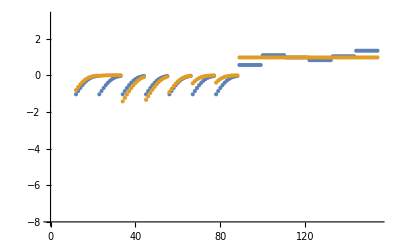

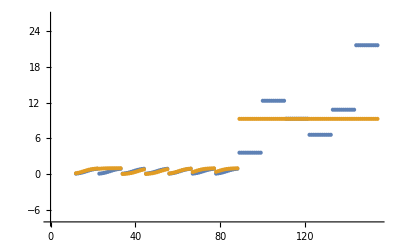

```mathematica
ListPlot[Log10[{fittingData[[All,-1]],filteredDataList[[1,3]]}], AxesOrigin->{0,-8}]
ListPlot[{fittingData[[All,-1]],filteredDataList[[1,3]]}, AxesOrigin->{0,-8}]
```

### Parameter Distribution

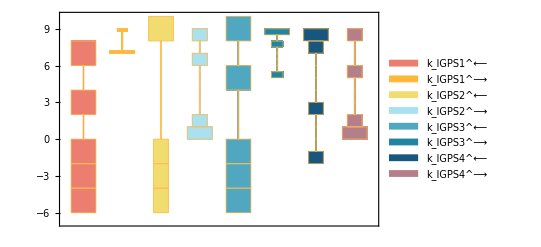

```mathematica
DistributionChart[Transpose[Log10[filteredDataList[[All,2]]]],ChartElementFunction->"HistogramDensity","PlotRange"->{-7,10},ChartLegends-> rateConstsSub[[All,2]]/.Reverse/@rateConstsSub,ChartStyle-> 24]
```

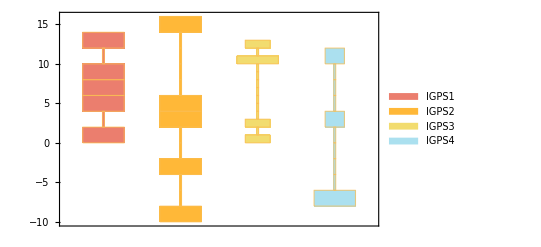

```mathematica
{ratios, plotLegend} = getElementaryKeqs[filteredDataList, rateConstsSub];
DistributionChart[Log10[Transpose@ratios],ChartElementFunction->"HistogramDensity",ChartLegends-> plotLegend,ChartStyle-> 24]
(*Histogram*)
```

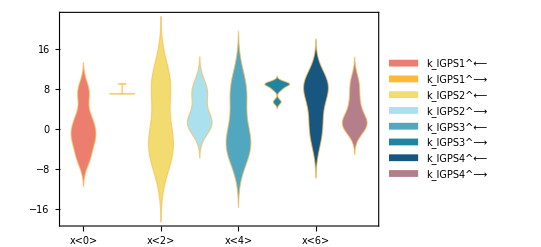

```mathematica
DistributionChart[Transpose[Log10[filteredDataList[[All,2]]]],ChartLabels-> rateConstsSub[[All,2]],"PlotRange"->{-7,10},ChartLegends-> rateConstsSub[[All,2]]/.Reverse/@rateConstsSub,ChartStyle-> 24](*Smooth*)(*If the distribution is narrow, the smooth Kernel outputs an error*)
```

### Data Error Distribution

```mathematica
errors=
Table[
	fittingData[[i,-1]]-filteredDataList[[j,3,i]],
 {j,1,Length@filteredDataList},{i,1,Length@filteredDataList[[1,3]]}];
```

```mathematica
funcNames=
Table[
	StringCases[func,RegularExpression[FileNameJoin[{inputPath , "(.*)\\.txt"}, OperatingSystem->$OperatingSystem]]->"$1"][[1]],{func,fittingData[[All,-2]]}]; (* fix later*);
```

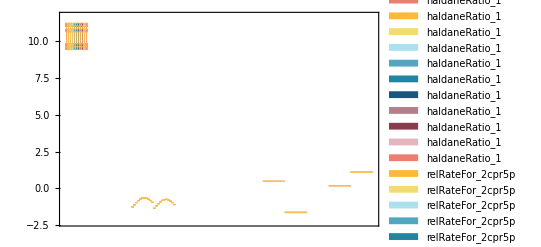

```mathematica
DistributionChart[Transpose[Log10[errors]],ChartElementFunction->"HistogramDensity",ChartLegends-> funcNames,ChartStyle-> 24](*Histogram*)
```

### Recalculate Enzyme Parameters for all Candidate Rate Constant Sets

```mathematica
enzymeSub= parameter[rxnName<>"_total"]-> 1;
assumedSaturatingConc=0.01;
paramSet = 1;
paramFitSub=Thread[rateConstsSub[[All,1]]->filteredDataList[[paramSet,2]]];
```

```mathematica
backCalculateKms[rxn, kmList, absoluteRateForward, absoluteRateReverse, paramFitSub, assumedSaturatingConc, rxnName]//TableForm
```

data value | predicted value | error in %
1.6×10^-6 | 8.78686×10^-7 | 45.0821
0.00009 | 8.78686×10^-7 | 99.0237
3.4×10^-7 | 8.78686×10^-7 | 158.437
4.2×10^-7 | 8.78686×10^-7 | 109.211
1.2×10^-6 | 8.78686×10^-7 | 26.7761
5.×10^-6 | 8.78686×10^-7 | 82.4263
5.8×10^-6 | 8.78686×10^-7 | 84.8502

```mathematica
Print[absoluteRateForward]
```

((3dhsk)^c nadph^c SHK3Dr_total_Global k_SHK3Dr1^⟶ k_SHK3Dr2^⟶ k_SHK3Dr3^⟶ k_SHK3Dr4^⟶ k_SHK3Dr5^⟶)/((3dhsk)^c k_SHK3Dr2^⟶ k_SHK3Dr3^⟶ k_SHK3Dr4^⟶ k_SHK3Dr5^⟶+k_SHK3Dr1^⟵ k_SHK3Dr2^⟶ (k_SHK3Dr3^⟵ (k_SHK3Dr4^⟶+k_SHK3Dr5^⟵)+k_SHK3Dr4^⟶ k_SHK3Dr5^⟶)+nadph^c k_SHK3Dr1^⟶ ((3dhsk)^c k_SHK3Dr3^⟶ k_SHK3Dr4^⟶ k_SHK3Dr5^⟶+k_SHK3Dr2^⟶ (k_SHK3Dr3^⟵ (k_SHK3Dr4^⟶+k_SHK3Dr5^⟵)+k_SHK3Dr4^⟶ k_SHK3Dr5^⟶+(3dhsk)^c k_SHK3Dr3^⟶ (k_SHK3Dr4^⟶+k_SHK3Dr5^⟵+k_SHK3Dr5^⟶))))

```mathematica
backCalculateKcats[rxn, kcatList, absoluteRateForward, absoluteRateReverse, paramFitSub, enzymeSub, assumedSaturatingConc]//TableForm
```

data value | predicted value | error in %
3.60337 | 9.27622 | 157.431
12.3115 | 9.27622 | 24.6542
9.3 | 9.27622 | 0.25574
6.60618 | 9.27622 | 40.4172
10.8101 | 9.27622 | 14.1895
21.6202 | 9.27622 | 57.0948

```mathematica
backCalculateRatios[customRatiosDataList[[1]][[2]], customRatiosDataList[[1]][[3]], paramFitSub]//TableForm
```

Part::partw: Part 1 of {} does not exist.

Part::partw: Part 3 of {}⟦1⟧ does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

data value | predicted value | error in %
{}⟦1⟧⟦3⟧ | 1 | (100 Abs[-1+{}⟦1⟧⟦3⟧])/({}⟦1⟧⟦3⟧)

```mathematica
backCalculateRatios[haldaneRatiosList[[1]], KeqList[[1]][[3]], paramFitSub]//TableForm
```

data value | predicted value | error in %
2.6×10^14 | 2.59997×10^14 | 0.00106687